## A. GetVariance[ns, nph,Δprior] function

(*Function modified for Feedback*)

```mathematica
GetVariance[NumShots_,NumPhotons_,Δprior_]:=
Block[{(*all variables in this function are global*)},
(*We first calculate the probabilities for the first shot then change index of s to the shot number*)
(*This block outputs the matrix of probabilities for multiple photons and 2 shots, row represents shot number*)
Clear[γs1,φ,r,θ,Pmϕ,Δ,run];
Clear["θ*"];
Clear["r*"];
(*Set accuracy*)
accuracy = 5;
(*Uncertainty prior to this shot*)
Δ = Δprior;
(*number of shots*)
ns=NumShots;
(* Number of Photons *)
nph =NumPhotons;
(* Flat Prior P(ϕ)*)
Pϕ = 1/Δ;
(* creation Subscript[a, 1] out† and Subscript[a, 2 out]†*)
aDagger = {a1Dagger, a2Dagger};
(* annihilation*)
a = {a1,a2};
(*rk here represents Subscript[r, k],magnitude of input state coefficient*)
r=Table[Table[Symbol["r"<>ToString[k]<>"s"<>ToString[l]],{k,0,nph}],{l,1,ns}];
(*θk here represents Subscript[θ, k],real phase of input state coefficient(exponent)*)
θ=Table[Table[Symbol["θ"<>ToString[k]<>"s"<>ToString[l]],{k,0,nph}],{l,1,ns}];
(*Subscript[φ, k] here represents Subscript[ϕ̃, k] or the unbiased phase estimator*)
φ=Table[Table[Symbol["φm"<>ToString[l]<>"m"<>ToString[n]],{l,0,nph}],{n,0,nph}];
(*Pmxϕsy represent the conditional probability: mx-> x^th outcome, sy-> y^th shot*)
Pmϕ = Table[Table[Symbol["Pm"<>ToString[k]<>"ϕs"<>ToString[n]],{k,0,nph}],{n,1,ns}];
(*Final beamsplitter*)
MatrixForm[u2s1={{Cos[γs1], Sin[γs1]},{-Sin[γs1],Cos[γs1]}}];
ketΨp=∑_(n=0)^nph (r⟦1,n+1⟧ ⅇ^(ⅈ θ⟦1,n+1⟧) ⅇ^(ⅈ (nph-n) ϕ) x1^(nph-n) x2^n)/(√n! √(nph-n)!);
(*Matrix multiplication substitution*)
sub2={x1->u2s1⟦1,1⟧a1Dagger+u2s1⟦2,1⟧a2Dagger,x2->u2s1⟦1,2⟧a1Dagger+u2s1⟦2,2⟧a2Dagger};
(*a1dagger goes to a1*)
sub3=Table[aDagger⟦n⟧->a⟦n⟧,{n,1,2}];
(*Phase sign change due to complex conjugation*)
sub4={ϕ->-ϕ};
(*Phase sign change due to complex conjugation*)
sub5=Table[Table[θ⟦k,n⟧->-θ⟦k,n⟧,{n,1,nph+1}],{k,1,ns}];
(*the ket mentioned below is at |ψ'''>, after the final beamsplitter*)
ketΨppp=ketΨp/.sub2;
braΨppp=ketΨppp/.sub3/.sub4/.sub5;
γs1 = Pi/4;
(*multiply coefficients of braΨppp *)
bracket=Table[(nph-n)!*n!*Coefficient[braΨppp ketΨppp,a1Dagger^n a2Dagger^(nph-n)a1^n a2^(nph-n)],{n,0,nph}];
(*Assigning values from the bracket matrix to the Probability matrix*)
MatrixForm[Table[Pmϕ[[1,n]]=bracket[[n,1]],{n,1,nph+1}] ];
(*This should show probabilities for shot 1 only*)
(*MatrixForm[Pmϕ];*)
(*Rows of Pmϕ correspond to shots and columns correspond to different outcomes*)
(*Pmϕ[[shot#, outcome#]]*)
(*Changing s1 to ss for all values of Pmϕ[[1,k]] to Pmϕ[[s,k]]*)
Subs = Table[Table[{r[[1,k]]-> r[[s,k]],θ[[1,k]]-> θ[[s,k]]},{k,1,nph+1}],{s,2,ns}];
(*Implimenting the substitution*)
Table[Table[Pmϕ[[shot,n]] = Pmϕ[[1,n]]/.Flatten[Subs[[shot-1]]],{n,1,nph+1}],{shot,2,ns}];
(*Clears elements of listOfϕ and listOfPmϕ for another run*)
Clear["ϕm*"];
(*List of possible outcomes as a list of strings - m0, m1 and so on...*)
AllOutcomes = Table[ToString[Symbol["m"<>ToString[n]]],{n,0,nph}];
(*Declaring all phase estimators*)
(*Starts with the base case of ϕ*)
ϕ1st ={"ϕ"} ;
(*Appends all possible m# to ϕ as shots require*)
(*e.g if ns=3 then this creates ϕm0m0m0, ϕm0m0m1 and so on*)
Table[ϕ1st = Outer[StringJoin,ϕ1st,AllOutcomes],ns];
(*Flattening this weird list of lists*)
listOfϕ=Flatten[ϕ1st];
(*Making each element of this list a symbol of its own, not doing this results in issues later*)
listOfϕ = Table[Symbol[listOfϕ[[j]]],{j,1,(nph+1)^ns}];
(*Need a better method of clearing the values assigned to variables in a list*)
Clear["aϕ*"];
(*Generates a list of dummy phase estimators*)
listOfaϕ =Table[Symbol["a"<>ToString[listOfϕ[[n]]]],{n,1,(nph+1)^ns}];
(*Generate a list of a product of probabilities that matches the outcome sequence*)
(*e.g outcome sequence m0m2m1 has the corresponding product of probabilities attached Pm0ϕs1*Pm2ϕs2*Pm1ϕs3 *)
(*converting trig expression to exponential form is important otherwise some parts later don't run*)
listOfPmϕ =Flatten[Outer[Times,Sequence@@Pmϕ]];
(*change this line*)
(*Split expressions into ϕ-dependent and ϕ-indepedent terms*)
(*Collecting terms by changing variables*)
If[nph==1,expr=Table[Table[Coefficient[listOfPmϕ[[n]],Exp[ⅈ ϕ],k],{k,0,ns*nph}],{n,1,(nph+1)^ns}];,
zzz=Table[Collect[listOfPmϕ[[n]]/.ϕ->Log[q]/I,q],{n,1,(nph+1)^ns}];
(*selecting correct coefficients for the correct exponent*)
GetOrder=Table[Table[Exponent[zzz[[n,j]],q],{j,1,Length[zzz[[n]]]}],{n,1,(nph+1)^ns}];
(*Find the ordering that sorts the lists*)
SetOrder=Table[Ordering[GetOrder[[n]]],{n,1,(nph+1)^ns}];
(*Converting sums into a list,because operators disturb the implementation of the ordering*)
zzzlist=Table[Flatten[Table[List[zzz[[m,n]]],{n,1,Length[zzz[[m]]]}]],{m,1,(nph+1)^ns}];
(*Check*)
(*Table[Table[Exponent[zzzlist[[n,j]],q],{j,1,Length[zzzlist[[n]]]}],{n,1,(nph+1)^ns}]*)
(*Implementing the ordering*)
zzzrearranged=Table[Flatten[Table[List[zzzlist[[m,n]]],{n,1,Length[zzzlist[[m]]]}]][[SetOrder[[m]]]],{m,1,(nph+1)^ns}];
(* Check*)(*exponentsRearranged=Table[Table[Exponent[zzzrearranged[[n,j]],q],{j,1,Length[zzzrearranged[[n]]]}],{n,1,(nph+1)^ns}];*)

(*Select positive exponents only*)
zzzselect=Table[Table[If[Exponent[zzzrearranged[[n,j]],q]<0,zzzrearranged[[n,j]]=0,zzzrearranged[[n,j]]],{j,1,Length[zzzrearranged[[n]]]}],{n,1,(nph+1)^ns}];
(*Delete the elements which match 0 (terms with negative exponent )*)
zzzselect=Table[DeleteCases[zzzselect[[n]],0],{n,1,(nph+1)^ns}];
(*Look-up table for zzzselect*)
exponentsSelected=Table[Table[Exponent[zzzselect[[n,j]],q],{j,1,Length[zzzselect[[n]]]}],{n,1,(nph+1)^ns}];
expr=zzzselect;];
(*If nph is even then run the next section, *)
If[EvenQ[nph],
(*Continue running if nph is even: to account for the abnormality of the middle term*)
middleTerm=((nph+1)^ns+1)/2;
numberOf0s=Count[exponentsSelected[[middleTerm]],0];
(*Give middleTerm the same dimensionality of the previous array*)
expr[[middleTerm]]=expr[[middleTerm-1]];
(*Check/Look-up table*)
(*Table[Exponent[expr1[[middleTerm,j]],q],{j,1,Length[expr1[[middleTerm]]]}]*)

(*collect all constants and put them in the 1st cell*)
expr[[middleTerm,1]]=Sum[zzzselect[[middleTerm,j]],{j,1,numberOf0s}];
(*Check/Look-up table*)
(* Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)

(*collect all coefficients for even kth exponents and overwrite them in the 2k+1th cell*)
Table[expr[[middleTerm,2i+1]]=zzzselect[[middleTerm,numberOf0s+i]],{i,1,ns*nph/2}];
(*Check/Look-up table*)
(*Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)

(*all coefficients for odd exponents set to 0 and overwrite them in the 2kth cell*)
Table[expr[[middleTerm,2i]]=0,{i,1,ns*nph/2}];
(*Check/Look-up table*)
(*Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)

(*Drop terms after the last if there are - There might not be...need to check, since we took care of dimensionality earlier*)
expr[[middleTerm]]=Drop[expr[[middleTerm]],{ns*nph+2,Length[expr[[middleTerm]]]}];
(*Check/Look-up table*)
(*Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)
(*else leave the expression alone*)
,expr];
(*Check*)
exponentsSelected2=Table[Table[Exponent[expr[[n,j]],q],{j,1,Length[expr[[n]]]}],{n,1,(nph+1)^ns}];
(*Print[exponentsSelected2];*)

expr=expr/.q->1;
(*expr[[n,k+1]] n is outcome number and k+1 is the coefficient of e^ikϕ*)
(*Splitting constant terms from the others and adding complex conjugate terms to the other - This is a check, not to be fed into the integral-*)
(* exprSplit =Table[expr[[n,1]]+2*Sum[expr[[n,k+1]]*E^(ⅈ k ϕ),{k,1,ns*nph}],{n,1,(nph+1)^ns}];*)
(*This list contains all the phase estimators*)
(*Removed integration and substituted pre-calculated integrals*)
listOfϕ1=ParallelTable[Re[(2*Sum[expr[[n,k+1]]*-((ⅈ (k Δ Cos[(k Δ)/2]-2 Sin[(k Δ)/2]))/k^2),{k,1,ns*nph}])]/Re[(expr[[n,1]]*Δ+2*Sum[expr[[n,k+1]]*((2 Sin[(k Δ)/2])/k),{k,1,ns*nph}])],{n,1,(nph+1)^ns}];
(*ParallelTable or something causes listOfϕ to get the order reversed as per our conventions, reverting it back*)
(*We calculate the final variance using the dummy phase estimators*)
(*Removed integration and substituted pre-calculated integrals*)
(*This list contains all the variance values*)
listOfPartialVariance1 = ParallelTable[Pϕ*Re[expr[[n,1]]*(Δ^3/12)+2*Sum[expr[[n,k+1]]*((4 k Δ Cos[(k Δ)/2]+(-8+k^2 Δ^2) Sin[(k Δ)/2])/(2 k^3)),{k,1,ns*nph}] -4*listOfaϕ[[n]]*Sum[expr[[n,k+1]]*-((ⅈ (k Δ Cos[(k Δ)/2]-2 Sin[(k Δ)/2]))/k^2),{k,1,ns*nph}]+Δ*expr[[n,1]]*listOfaϕ[[n]]^2+2*listOfaϕ[[n]]^2*Sum[expr[[n,k+1]]*((2 Sin[(k Δ)/2])/k),{k,1,ns*nph}] ],{n,1,(nph+1)^ns}];
(*We calculated the final variance using the dummy phase estimators - listOfaϕ*)
(*And then replace the dummy phase estimators in 1.3.3 by the real ones calculated in 1.3.2*)
dummyFinalVariance1=Flatten[listOfPartialVariance1/.{Table[listOfaϕ[[n]]-> listOfϕ1[[n]],{n,1,(nph+1)^ns}]},1];

(*Normalizing the variance, each product normalizes 1 probability term in the product (of listOfPmϕ); e.g (1 /(r0s1^2+r1s1^2+r2s1^2)) normalizes Pm#ϕs1*)
normalizationTerm = ∏_(i=1)^ns 1/(∑_(s=1)^(nph+1) (r[[i,s]])^2);
(*Final variance*)
(*Sum is replaced by ParallelSum to decrease the time of computation*)
(*Note: We are ommitting Pϕ here since we have already taken that into consideration earlier while constructing dummyfinalvariance*)
finalVariance= normalizationTerm*Sum[dummyFinalVariance1[[j]], {j,1,(nph+1)^ns}];
(*While the imaginary term is essentially 0, mathematica may be calculating some expressions analytically and would keep ~0 imaginary values, therefore neglecting those*)
finalVariance = Re[finalVariance];
(* Print[finalVariance]; *)
Return[finalVariance]
(*Manual sanity check - Need to make it automatic*)
(*Print[Simplify[finalVariance/.{r0s1-> 1,r1s1-> 0,r2s1-> 0,r0s2-> 1,r1s2-> 0,r2s2-> 0},Assumptions-> Δ∈Reals]];*)]
```

## B. ExtractOptState[delta,postVariance] Function

(*In case it takes too long change this version from 2.5 in that it simplifies optimization taking symmetry of states into account *)

```mathematica
ExtractOptState[delta_,PostVariance_]:=
(*Block or Module*)
Block[{Δ,OptimalrValues,variablelist,ListOfOptimalrValues,variablelistrandom,nrun,iteration,OptimalVariance,listforfindminimum,listOfLocalMinVariance,IndexMinVar,finalVariance},(*{"θ*","r*",(*list variables to keep local*)}*)
(*Generate a list to optimize over*)
Δ=delta;
finalVariance = PostVariance;
variablelist = Flatten[{θ,r}];
(*Generate a list of dummy optimization variable to assign a random starting point to them*)
variablelistrandom = ParallelTable[Symbol[ToString[variablelist[[l]]]<>"dummy"],{l,1,2*ns*(nph+1)}];
(*Give a random starting point to each dummy variable; θs are between -π and π while rs are between 0 and 1*)
(*run 50 iterations of findminimum*)
(*MaxIterations->∞;*)
nrun=20;
iteration=ParallelTable[
SeedRandom[];
Table[variablelistrandom[[n]] =RandomReal[{-π,π}],{n,1,ns*(nph+1)}];
Table[variablelistrandom[[n]] =RandomReal[{0,1}],{n,ns*(nph+1)+1,2*ns*(nph+1)}];
(*Arranging listforfindminimum to match FindMinimum syntax*)
listforfindminimum = Table[{variablelist[[n]],variablelistrandom[[n]]},{n,1,2*ns*(nph+1)}];
(*Print[listforfindminimum];*)
(*Optimization*)
(*Print[finalVariance];*)
FindMinimum[finalVariance,listforfindminimum,AccuracyGoal-> 5],{n,1,nrun}];
(*lower accuracy in case it takes too long*)
(*Print[iteration];*)
(*Finds the minimum from list of local minimums*)
listOfLocalMinVariance=Table[iteration[[n,1]],{n,1,nrun}];
IndexMinVar =Position[listOfLocalMinVariance,Min[listOfLocalMinVariance]]⟦1,1⟧;
OptimalVariance={iteration[[IndexMinVar,1]],Table[iteration[[IndexMinVar,2,n]],{n,1,Length[iteration[[IndexMinVar,2]]]}]};
(*Print[OptimalVariance];*)
(*Do we ignore the error we get in certain cases?*)
(*Extract minvalues for r variables*)
(*rcheck=Table[OptimalVariance[[2,n,1]],{n,ns*(nph+1)+1,Length[OptimalVariance[[2]]]}];*)
ListOfOptimalrValues=Table[OptimalVariance[[2,n,2]],{n,ns*(nph+1)+1,Length[OptimalVariance[[2]]]}];
(*Print[rcheck];*)
(*Partition lists into seperate shots*)
(*rchecksplit=Partition[rcheck,nph+1];*)
OptimalrValues=Partition[ListOfOptimalrValues,nph+1];
(*Normalizing over multiple shots*)
OptimalrValues = Table[Abs[Normalize[OptimalrValues[[n]]]],{n,1,ns}];
(*Print[OptimalrValues];*)
(*Return[OptimalrValues]*)
(*Print[rchecksplit];*)
(*plot[[plotnumber]]=Table[ListLinePlot[OptimalrValues[[n]],PlotLegends-> {OptimalVariance[[1]]},PlotLabel->Δ],{n,1,ns}]*)
Return[OptimalVariance];]
```

## C. Plug States

### VarRatioOptimal

```mathematica
GetOpt[]:=Block[{},VarRatioOpt=Table[Δ =n/10*π;
finalVarianceOpt=ExtractOptState[Δ,finalVariance];
finalVarianceOpt/Δ^2/12
(*,{n,{1,3,5,10}}];*)
,{n,1,10}];
Return[VarRatioOpt];]
```

### Plug in N00N states and compare optimal variance with the new variance

```mathematica
PlugN00NSBS[]:=
Block[{},
(*feed in θ values*)
sublistN00Nθ = Table[Table[θ[[n,i]] ->  RandomReal[{-π,π}],{i,1,nph+1}],{n,1,ns}];
Table[sublistN00Nθ[[n,nph+1,2]]= sublistN00Nθ[[n,1,2]]-π/2,{n,1,ns}];
sublistN00Nθ;
(*feed in r values*)
sublistN00Nr=Table[Table[If[i==1 ||i==nph+1,r[[n,i]]-> 1/(√2) ,r[[n,i]]->0 ],{i,1,nph+1}],{n,1,ns}];
substlistN00N = Flatten[{sublistN00Nθ, sublistN00Nr}];
finalVarianceN00N=finalVariance/.substlistN00N;
(*Print[finalVarianceN00N/finalVarianceN00NOpt];*)
(*Print[substlistN00N];*)
(*returns the variance and state to be plugged in*)
Return[{finalVarianceN00N,substlistN00N}];]
```

### Plug in Gaussian (G1) c_p≃0.14, ρ≃c_p Δ/N

```mathematica
PlugG1SBS[]:=
Block[{},Clear[ρ3];
ρ3 = Table[Symbol["ρ3s"<>ToString[n]],{n,1,ns}];
Table[ρ3[[n]]=0.16Δ/nph;,{n,1,ns}];
ψG1r =Table[Table[(E^(-ρ3[[n]](k-nph/2)^2))/(√(∑_(kprime=0)^nph (E^(-ρ3[[n]](kprime-nph/2)^2))^2)),{k,0,nph}],{n,1,ns}];
ψG1θ=Table[Table[ k (π/2),{k,0,nph}],{n,1,ns}];
substlistG1r=Table[Table[r[[n,i]]-> ψG1r[[n,i]],{i,1,nph+1}],{n,1,ns}];
substlistG1θ = Table[Table[θ[[n,i]]-> ψG1θ[[n,i]],{i,1,nph+1}],{n,1,ns}];
substlistG1= Flatten[{substlistG1θ,substlistG1r}];
finalVarianceG1=finalVariance/.substlistG1;
(*Print[OptimalVarianceQG2];*)
(*this prints out optimized ρ and ρprime values*)
(*finalVarianceQG2[[2]]*)
(*Print[substlistG1];*)
(*This returns the state to be plugged in*)
Return[{finalVarianceG1,substlistG1}];];
```

## D. PostVarianceOptsbs[nph] function - Returns shot 1 and shot 2 optimal states

```mathematica
PostVarianceOptsbs[nph_]:=Block[{PostShotVarOptRatio,PostShot1Variance,numPho,PostShot1OptState,PostShot1OptΔ,PostShot2Variance,PostShot2OptState,uncertainty},
PostShotVarOptRatio=Table[uncertainty = (num*π)/10;
Clear[Δ];
numPho=nph;
PostShot1Variance = GetVariance[1,numPho,Δ];
(*Find variance after 1 shot Variance(Δ), plug that into ExtractOptState to return the optimized numerical value for Variance*)
PostShot1OptState = ExtractOptState[uncertainty,PostShot1Variance];
(*Calculate uncertainty post shot 1*)
PostShot1OptΔ = √(12*PostShot1OptState[[1]]);
(*Replace post shot 1 optimal state as input into 2nd shot*)
PostShot2Variance = GetVariance[1,numPho,PostShot1OptΔ];
PostShot2OptState = ExtractOptState[PostShot1OptΔ,PostShot2Variance];
{PostShot1OptState,PostShot2OptState}
(*PostShot2OptState[[1]]/(uncertainty^2/12)*),{num,1,10}];
Return[PostShotVarOptRatio];]
```

## E. PostVariancesbs[nph,Δd] - Returns appropriate (apt) states for shot 1 and shot 2

```mathematica
PostVariancesbs[nph_,Δd_]:=Block[{(*PostShotVarRatio,PostShot1Variance,numPho,PostShot1State,PostShot1Δ,PostShot2Variance,PostShot2State,uncertainty*)},
Clear[Δ];
numPho=nph;
Δ=Δd;
uncertainty = Δ;
PostShot1Variance = GetVariance[1,numPho,Δ];
(*Plug N00N in N00N regime*)
(*Plug Gaussian in Gaussian regime*)
If[Δ*numPho> 5,PostShot1State=PlugG1SBS[];(*Print["Gaussian"];*),PostShot1State=PlugN00NSBS[];(*Print["N00N"];*)];
(*Calculate uncertainty post shot 1*)
PostShot1Δ = √(12*PostShot1State[[1]]);
(*Replace post shot 1 optimal state as input into 2nd shot*)
PostShot2Variance = GetVariance[1,numPho,PostShot1Δ];
(*Plug N00N in N00N regime*)
(*Plug Gaussian in Gaussian regime*)
If[PostShot1Δ*numPho> 5,PostShot2State=PlugG1SBS[];(*Print["Gaussian"];*),PostShot2State=PlugN00NSBS[];(*Print["N00N"];*)];
(*PostShotVarRatio=PostShot2State/(uncertainty^2/12);*)
(*Return the states for each of the two shots*)
(*Print[{PostShot1State,PostShot2State}];*)
Return[{PostShot1State,PostShot2State}];]
```

## 1. Results

## Comparing ratio of Post-shot variance for 2 shots (SBS optimization with Global optimization)

#### Post - Shot Variance (Δ) for Nph = 4

```mathematica
nph = 4
```

4

```mathematica
(*Gives variance as well as the optimal state for each of the shots*)
PostShotVarOptRatio4=PostVarianceOptsbs[nph];
(*Gather optimal states for each of the shots individually*)
(*For the first shot*)
Shot1OptStateList = Table[PostShotVarOptRatio4[[n,1,2]],{n,1,10}];
(*For the second shot*)
Shot2OptStatetempList = Table[PostShotVarOptRatio4[[n,2,2]],{n,1,10}];
(*We want to plug in these individually optimized states into the globally optimized variance to fix assumption about the shape of the uncertainty distribution of 2nd shot being flat*)
Clear[Δ];
Variance26 = GetVariance[2,nph,Δ];
(*Optimization for 2 shots*)
VarRatioOptimal4 = GetOpt[];
VRO5=Table[VarRatioOptimal4[[n,1]] ,{n,1,10}];
(*VRO5 is the globally optimized ratio of variance to the prior variance*)
(*Variance24 in function of states,phases and Δ*)
(*Change variable names for second shot*)

Shot2OptStateList=Table[Flatten[Table[{θ[[2,n]]-> Shot2OptStatetempList[[s,n,2]],r[[2,n]]-> Shot2OptStatetempList[[s,n+nph+1,2]]},{n,1,nph+1}]],{s,1,10}];

(*Substitution list*)
OptimalStates = Table[Join[Shot1OptStateList[[s]],Shot2OptStateList[[s]]],{s,1,10}];
(*Clear Δ to make sure that Variance 24 in function of states, phases and Δ*)
Clear[Δ];
(*Plug in optimal state into the 2 shot variance formula*)
PostShotVarOptRatio5 =Table[(Variance26/.Join[OptimalStates[[n]],{Δ-> (n*π)/10}])/(((n*π)/10)^2/12),{n,1,10}];
```

```mathematica
PostShotVarOptRatio5
```

{0.783255,0.449095,0.29166,0.294896,0.341544,0.265612,0.204719,0.175969,0.156079,0.135914}

```mathematica
VRO5
```

{0.783255,0.449095,0.29166,0.260586,0.240654,0.193933,0.15679,0.132188,0.115589,0.102854}

```mathematica
VRO5={0.692726578791068,0.34297713570026084,0.27011415914404185,0.23307169722889842,0.1936515681862858,0.15180192330137504,0.123342121711852,0.10363692148034079,0.09129116117913245,0.08208712442913292}
```

{0.692727,0.342977,0.270114,0.233072,0.193652,0.151802,0.123342,0.103637,0.0912912,0.0820871}

```mathematica
PostShotVarOptRatio5
```

```mathematica
PostShotVarOptRatio5={0.6927265787910466,0.3429771357002114,0.2924879226351906,0.3274523661067626,0.25795427526335474,0.19241295314115003,0.161002102250986,0.1355189796966908,0.11833509080849251,0.10941296823849399}
```

{0.692727,0.342977,0.292488,0.327452,0.257954,0.192413,0.161002,0.135519,0.118335,0.109413}

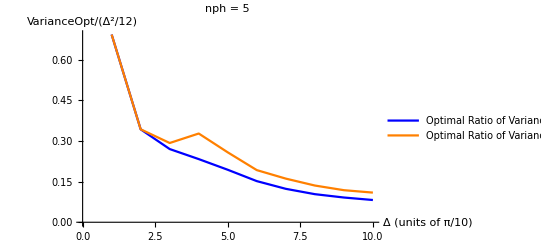

```mathematica
Show[ListLinePlot[VRO5,PlotLabel-> "nph = 5",PlotStyle->Blue,PlotLegends->{"Optimal Ratio of Variance 2 shot"}],ListLinePlot[PostShotVarOptRatio5,PlotLegends->{"Optimal Ratio of Variance 2 shot (sbs)"},PlotStyle->Orange],AxesLabel-> {"Δ (units of π/10)","VarianceOpt/(Δ^2/12)"}]
```

## Comparing sbs where states are plugged in with all shots together for 2 shots - Nph = 5

```mathematica
(*Again, plug PostShot1State and PostShot2State into the 2 shot variance*)
(*The 2shot variance in function of Δ*)
Clear[Δ];
Variance26;
(*Apt states that need to be plugged into 2 shot global variance. Aptness is decided by the boundaries*)
PlugStates=Table[PostVariancesbs[5,n*π/10],{n,1,10}];
(*PlugStates contains information of the variance post shot 1 and post shot 2 as well as the apt input states for both shots*)
(*Gather apt states for each of the shots individually*)
(*For the first shot*)
Shot1AptStateList = Table[PlugStates[[n,1,2]],{n,1,10}];
(*For the second shot*)
Shot2AptStatetempList = Table[PlugStates[[n,2,2]],{n,1,10}];
(*We want to plug in these individually optimized states into the globally optimized variance to fix assumption about the shape of the uncertainty distribution of 2nd shot being flat*)
Clear[Δ];
Variance26 = GetVariance[2,5,Δ];
(*Optimization for 2 shots*)
(*Change variable names for second shot*)
Shot2AptStateList=Table[Flatten[Table[{θ[[2,n]]-> Shot2AptStatetempList[[s,n,2]],r[[2,n]]-> Shot2AptStatetempList[[s,n+nph+1,2]]},{n,1,nph+1}]],{s,1,10}];
(*Substitution list*)
AptStates = Table[Join[Shot1AptStateList[[s]],Shot2AptStateList[[s]]],{s,1,10}];
(*Clear Δ to make sure that Variance 24 in function of states, phases and Δ*)
Clear[Δ]
VR5 = Table[(Variance26/.Join[AptStates[[n]],{Δ-> (n*π)/10}])/((n*π)/10)^2/12,{n,1,10}];
```

```mathematica
(*VRO5 - Global optimal non-adaptive variance ratio*)
GetVariance[2,5,Δ];
```

```mathematica
VarRatioOptimal5 = GetOpt[]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
VRO5=Table[VarRatioOptimal5[[n,1]] ,{n,1,10}];
```

```mathematica
VRO5={0.6927265787912112,0.34297713570121713,0.26995313162674117,0.23371235912746216,0.19365156818603607,0.15180192329997858,0.12334212171216266,0.10363692148031488,0.09129116117958291,0.08208712442898417}
```

{0.692727,0.342977,0.269953,0.233712,0.193652,0.151802,0.123342,0.103637,0.0912912,0.0820871}

```mathematica
VR5
```

```mathematica
VR5={0.6927265787909833,0.3429771357002025,0.31735097014621383,0.340952469102649,0.2954497160386965,0.2270389359259946,0.12478294156950283,0.10520515684148408,0.093283029547975,0.08479199880729761}
```

{0.692727,0.342977,0.317351,0.340952,0.29545,0.227039,0.124783,0.105205,0.093283,0.084792}

```mathematica
PostShotVarOptRatio5={0.6927265787910466,0.3429771357002114,0.2924879226351906,0.3274523661067626,0.25795427526335474,0.19241295314115003,0.161002102250986,0.1355189796966908,0.11833509080849251,0.10941296823849399}
```

{0.692727,0.342977,0.292488,0.327452,0.257954,0.192413,0.161002,0.135519,0.118335,0.109413}

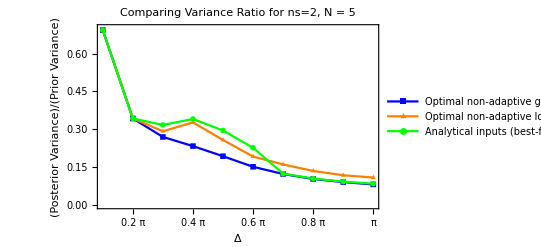

```mathematica
Show[ListLinePlot[VRO5,PlotMarkers ->{■,Scaled[0.05]},PlotStyle->Blue,PlotLegends->Placed[{"Optimal non-adaptive global"},{0.5,0.9}]],ListLinePlot[PostShotVarOptRatio5,PlotMarkers ->{▲,Scaled[0.05]},PlotLegends->Placed[{"Optimal non-adaptive local (shot-by-shot)"},{0.5,0.8}],PlotStyle->Orange],ListLinePlot[VR5,PlotMarkers ->{•,Scaled[0.05]},PlotLegends->Placed[{"Analytical inputs (best-fit)"},{0.5,0.7}],PlotStyle->Green],PlotLabel-> "Comparing Variance Ratio for ns=2, N = 5",Frame->True,FrameLabel-> {"Δ","(Posterior Variance)/(Prior Variance)"},PlotRange->{{1,10},{0,0.7}},FrameTicks->{{Automatic,Automatic},{{{2,"0.2 π"},{4,"0.4 π"},{6,"0.6 π"},{8,"0.8 π"},{10,"π"}},Automatic}}]
```

```mathematica
RatioPlugAptvsOptimal=Table[VR5[[n]]/VRO5[[n]],{n,1,10}]
```

{1.,1.,1.17652,1.46287,1.52568,1.49563,1.01168,1.01513,1.02182,1.03295}

```mathematica
RatioOptsbsvsOptimal=Table[PostShotVarOptRatio5[[n]]/VRO5[[n]],{n,1,10}]
```

{1.,1.,1.08434,1.40494,1.33205,1.26753,1.30533,1.30763,1.29624,1.33289}

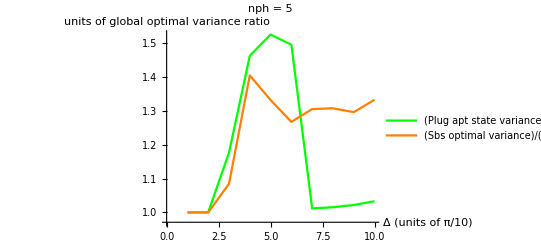

```mathematica
Show[ListLinePlot[RatioPlugAptvsOptimal,PlotLabel-> "nph = 5",PlotStyle->Green,PlotLegends->{"(Plug apt state variance)/(global optimal variance)"}],ListLinePlot[RatioOptsbsvsOptimal,PlotLegends->{"(Sbs optimal variance)/(global optimal variance)"},PlotStyle->Orange],AxesLabel-> {"Δ (units of π/10)","units of global optimal variance ratio"}]
```

## Comparing sbs where states are plugged in with all shots together for 2 shots - Nph = 4

```mathematica
(*Again, plug PostShot1State and PostShot2State into the 2 shot variance*)
(*The 2shot variance in function of Δ*)
Clear[Δ];
Variance26;
(*Apt states that need to be plugged into 2 shot global variance. Aptness is decided by the boundaries*)
PlugStates=Table[PostVariancesbs[4,n*π/10],{n,1,10}];
(*PlugStates contains information of the variance post shot 1 and post shot 2 as well as the apt input states for both shots*)
(*Gather apt states for each of the shots individually*)
(*For the first shot*)
Shot1AptStateList = Table[PlugStates[[n,1,2]],{n,1,10}];
(*For the second shot*)
Shot2AptStatetempList = Table[PlugStates[[n,2,2]],{n,1,10}];
(*We want to plug in these individually optimized states into the globally optimized variance to fix assumption about the shape of the uncertainty distribution of 2nd shot being flat*)
Clear[Δ];
Variance26 = GetVariance[2,4,Δ];
(*Optimization for 2 shots*)
(*Change variable names for second shot*)
Shot2AptStateList=Table[Flatten[Table[{θ[[2,n]]-> Shot2AptStatetempList[[s,n,2]],r[[2,n]]-> Shot2AptStatetempList[[s,n+nph+1,2]]},{n,1,nph+1}]],{s,1,10}];
(*Substitution list*)
AptStates = Table[Join[Shot1AptStateList[[s]],Shot2AptStateList[[s]]],{s,1,10}];
(*Clear Δ to make sure that Variance 24 in function of states, phases and Δ*)
Clear[Δ]
VR4 = Table[(Variance26/.Join[AptStates[[n]],{Δ-> (n*π)/10}])/((n*π)/10)^2/12,{n,1,10}];
```

```mathematica
(*VR5 is the optimal shot-by-shot variance ratio*)
```

```mathematica
VR4
```

{0.783255,0.449095,0.29166,0.327742,0.325623,0.286739,0.231896,0.186204,0.117103,0.105124}

```mathematica
(*VRO5 - Global optimal non-adaptive variance ratio*)
```

```mathematica
GetVariance[2,4,Δ];
```

```mathematica
VarRatioOptimal4 = GetOpt[];
VRO4=Table[VarRatioOptimal4[[n,1]] ,{n,1,10}];
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
VRO4
```

{0.783255,0.449095,0.29166,0.258841,0.240654,0.193933,0.15679,0.132188,0.115589,0.102854}

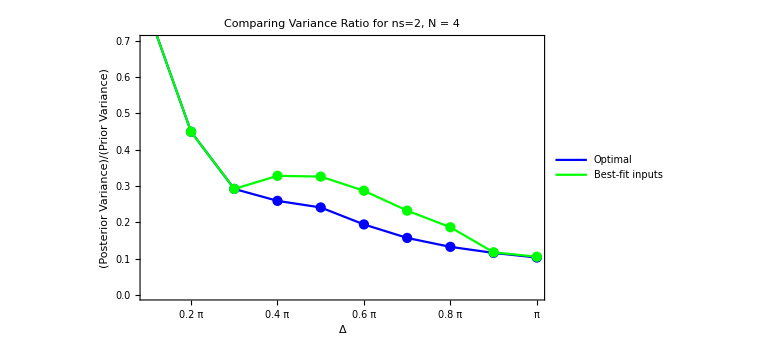

```mathematica
Show[ListPlot[VRO4,PlotStyle->Blue,PlotLabel-> "Comparing Variance Ratio for ns=2, N = 4"],ListLinePlot[VRO4,PlotStyle->Blue,PlotLegends->{"Optimal"}],(*ListPlot[PostShotVarOptRatio5,PlotStyle->Orange],ListLinePlot[PostShotVarOptRatio5,PlotLegends->{"Optimal Feedback"},PlotStyle->Orange],*)ListPlot[VR4,PlotStyle->Green],ListLinePlot[VR4,PlotLegends->{"Best-fit inputs"},PlotStyle->Green],Frame->True,FrameLabel-> {"Δ","(Posterior Variance)/(Prior Variance)"},PlotRange->{{1,10},{0,0.7}},FrameTicks->{{Automatic,Automatic},{{{2,"0.2 π"},{4,"0.4 π"},{6,"0.6 π"},{8,"0.8 π"},{10,"π"}},Automatic}},ImageSize->Large]
```

```mathematica
RatioPlugAptvsOptimal=Table[VR5[[n]]/VRO5[[n]],{n,1,10}]
```

{1.,1.,1.17652,1.46287,1.52568,1.49563,1.01168,1.01513,1.02182,1.03295}

```mathematica
RatioOptsbsvsOptimal=Table[PostShotVarOptRatio5[[n]]/VRO5[[n]],{n,1,10}]
```

{1.,1.,1.08434,1.40494,1.33205,1.26753,1.30533,1.30763,1.29624,1.33289}

```mathematica
Show[ListLinePlot[RatioPlugAptvsOptimal,PlotLabel-> "nph = 5",PlotStyle->Green,PlotLegends->{"(Plug apt state variance)/(global optimal variance)"}],ListLinePlot[RatioOptsbsvsOptimal,PlotLegends->{"(Sbs optimal variance)/(global optimal variance)"},PlotStyle->Orange],AxesLabel-> {"Δ (units of π/10)","units of global optimal variance ratio"}]
```

-Graphics-

## Fisher Information of Gaussians and N00Ns

```mathematica
PostVariancesbs[nph_,Δd_]:=Block[{(*PostShotVarRatio,PostShot1Variance,numPho,PostShot1State,PostShot1Δ,PostShot2Variance,PostShot2State,uncertainty*)},
Clear[Δ];
numPho=nph;
Δ=Δd;
uncertainty = Δ;
PostShot1Variance = GetVariance[1,numPho,Δ];
(*Plug N00N in N00N regime*)
(*Plug Gaussian in Gaussian regime*)
If[Δ*numPho> 5,PostShot1State=PlugG1SBS[];(*Print["Gaussian"];*),PostShot1State=PlugN00NSBS[];(*Print["N00N"];*)];
(*Calculate uncertainty post shot 1*)
PostShot1Δ = √(12*PostShot1State[[1]]);
(*P(m|ϕ)*)
Pmϕ=listOfPmϕ/.PostShot1State[[2]];
Return[{PostShot1State,Pmϕ}];]
```

```mathematica
(*p(m|ϕ)*)
```

```mathematica
likelihoodFn=PostVariancesbs[3,π/10][[2]]
```

{1/6 ((0.246554-0.560546 ⅈ)-1/2 √(3/2) ⅇ^((0.-2.72721 ⅈ)-3 ⅈ ϕ)) ((0.246554+0.560546 ⅈ)-1/2 √(3/2) ⅇ^((0.+2.72721 ⅈ)+3 ⅈ ϕ)),1/2 ((0.246554-0.560546 ⅈ)+1/2 √(3/2) ⅇ^((0.-2.72721 ⅈ)-3 ⅈ ϕ)) ((0.246554+0.560546 ⅈ)+1/2 √(3/2) ⅇ^((0.+2.72721 ⅈ)+3 ⅈ ϕ)),1/2 ((0.246554-0.560546 ⅈ)-1/2 √(3/2) ⅇ^((0.-2.72721 ⅈ)-3 ⅈ ϕ)) ((0.246554+0.560546 ⅈ)-1/2 √(3/2) ⅇ^((0.+2.72721 ⅈ)+3 ⅈ ϕ)),1/6 ((0.246554-0.560546 ⅈ)+1/2 √(3/2) ⅇ^((0.-2.72721 ⅈ)-3 ⅈ ϕ)) ((0.246554+0.560546 ⅈ)+1/2 √(3/2) ⅇ^((0.+2.72721 ⅈ)+3 ⅈ ϕ))}

```mathematica
(*ln p(m|ϕ)*)
```

```mathematica
logLikelihoodFn=Log[likelihoodFn]
```

{Log[1/6 ((0.246554-0.560546 ⅈ)-1/2 √(3/2) ⅇ^((0.-2.72721 ⅈ)-3 ⅈ ϕ)) ((0.246554+0.560546 ⅈ)-1/2 √(3/2) ⅇ^((0.+2.72721 ⅈ)+3 ⅈ ϕ))],Log[1/2 ((0.246554-0.560546 ⅈ)+1/2 √(3/2) ⅇ^((0.-2.72721 ⅈ)-3 ⅈ ϕ)) ((0.246554+0.560546 ⅈ)+1/2 √(3/2) ⅇ^((0.+2.72721 ⅈ)+3 ⅈ ϕ))],Log[1/2 ((0.246554-0.560546 ⅈ)-1/2 √(3/2) ⅇ^((0.-2.72721 ⅈ)-3 ⅈ ϕ)) ((0.246554+0.560546 ⅈ)-1/2 √(3/2) ⅇ^((0.+2.72721 ⅈ)+3 ⅈ ϕ))],Log[1/6 ((0.246554-0.560546 ⅈ)+1/2 √(3/2) ⅇ^((0.-2.72721 ⅈ)-3 ⅈ ϕ)) ((0.246554+0.560546 ⅈ)+1/2 √(3/2) ⅇ^((0.+2.72721 ⅈ)+3 ⅈ ϕ))]}

```mathematica
(*(∂ log p(m|ϕ))/(∂ϕ)*)
```

```mathematica
pprime=D[logLikelihoodFn,ϕ]
```

{(6 (-1/4 ⅈ √(3/2) ⅇ^((0.+2.72721 ⅈ)+3 ⅈ ϕ) ((0.246554-0.560546 ⅈ)-1/2 √(3/2) ⅇ^((0.-2.72721 ⅈ)-3 ⅈ ϕ))+1/4 ⅈ √(3/2) ⅇ^((0.-2.72721 ⅈ)-3 ⅈ ϕ) ((0.246554+0.560546 ⅈ)-1/2 √(3/2) ⅇ^((0.+2.72721 ⅈ)+3 ⅈ ϕ))))/(((0.246554-0.560546 ⅈ)-1/2 √(3/2) ⅇ^((0.-2.72721 ⅈ)-3 ⅈ ϕ)) ((0.246554+0.560546 ⅈ)-1/2 √(3/2) ⅇ^((0.+2.72721 ⅈ)+3 ⅈ ϕ))),(2 (3/4 ⅈ √(3/2) ⅇ^((0.+2.72721 ⅈ)+3 ⅈ ϕ) ((0.246554-0.560546 ⅈ)+1/2 √(3/2) ⅇ^((0.-2.72721 ⅈ)-3 ⅈ ϕ))-3/4 ⅈ √(3/2) ⅇ^((0.-2.72721 ⅈ)-3 ⅈ ϕ) ((0.246554+0.560546 ⅈ)+1/2 √(3/2) ⅇ^((0.+2.72721 ⅈ)+3 ⅈ ϕ))))/(((0.246554-0.560546 ⅈ)+1/2 √(3/2) ⅇ^((0.-2.72721 ⅈ)-3 ⅈ ϕ)) ((0.246554+0.560546 ⅈ)+1/2 √(3/2) ⅇ^((0.+2.72721 ⅈ)+3 ⅈ ϕ))),(2 (-3/4 ⅈ √(3/2) ⅇ^((0.+2.72721 ⅈ)+3 ⅈ ϕ) ((0.246554-0.560546 ⅈ)-1/2 √(3/2) ⅇ^((0.-2.72721 ⅈ)-3 ⅈ ϕ))+3/4 ⅈ √(3/2) ⅇ^((0.-2.72721 ⅈ)-3 ⅈ ϕ) ((0.246554+0.560546 ⅈ)-1/2 √(3/2) ⅇ^((0.+2.72721 ⅈ)+3 ⅈ ϕ))))/(((0.246554-0.560546 ⅈ)-1/2 √(3/2) ⅇ^((0.-2.72721 ⅈ)-3 ⅈ ϕ)) ((0.246554+0.560546 ⅈ)-1/2 √(3/2) ⅇ^((0.+2.72721 ⅈ)+3 ⅈ ϕ))),(6 (1/4 ⅈ √(3/2) ⅇ^((0.+2.72721 ⅈ)+3 ⅈ ϕ) ((0.246554-0.560546 ⅈ)+1/2 √(3/2) ⅇ^((0.-2.72721 ⅈ)-3 ⅈ ϕ))-1/4 ⅈ √(3/2) ⅇ^((0.-2.72721 ⅈ)-3 ⅈ ϕ) ((0.246554+0.560546 ⅈ)+1/2 √(3/2) ⅇ^((0.+2.72721 ⅈ)+3 ⅈ ϕ))))/(((0.246554-0.560546 ⅈ)+1/2 √(3/2) ⅇ^((0.-2.72721 ⅈ)-3 ⅈ ϕ)) ((0.246554+0.560546 ⅈ)+1/2 √(3/2) ⅇ^((0.+2.72721 ⅈ)+3 ⅈ ϕ)))}

```mathematica
(*find phitilde*)
```

```mathematica
FI=Re[Sum[pprime[[n]]^2 likelihoodFn[[n]],{n,1,nph+1}]]
```

Re[(6 (-1/4 ⅈ √(3/2) ⅇ^((0.+2.72721 ⅈ)+3 ⅈ ϕ) ((0.246554-0.560546 ⅈ)-1/2 √(3/2) ⅇ^((0.-2.72721 ⅈ)-3 ⅈ ϕ))+1/4 ⅈ √(3/2) ⅇ^((0.-2.72721 ⅈ)-3 ⅈ ϕ) ((0.246554+0.560546 ⅈ)-1/2 √(3/2) ⅇ^((0.+2.72721 ⅈ)+3 ⅈ ϕ)))^2)/(((0.246554-0.560546 ⅈ)-1/2 √(3/2) ⅇ^((0.-2.72721 ⅈ)-3 ⅈ ϕ)) ((0.246554+0.560546 ⅈ)-1/2 √(3/2) ⅇ^((0.+2.72721 ⅈ)+3 ⅈ ϕ)))+(2 (-3/4 ⅈ √(3/2) ⅇ^((0.+2.72721 ⅈ)+3 ⅈ ϕ) ((0.246554-0.560546 ⅈ)-1/2 √(3/2) ⅇ^((0.-2.72721 ⅈ)-3 ⅈ ϕ))+3/4 ⅈ √(3/2) ⅇ^((0.-2.72721 ⅈ)-3 ⅈ ϕ) ((0.246554+0.560546 ⅈ)-1/2 √(3/2) ⅇ^((0.+2.72721 ⅈ)+3 ⅈ ϕ)))^2)/(((0.246554-0.560546 ⅈ)-1/2 √(3/2) ⅇ^((0.-2.72721 ⅈ)-3 ⅈ ϕ)) ((0.246554+0.560546 ⅈ)-1/2 √(3/2) ⅇ^((0.+2.72721 ⅈ)+3 ⅈ ϕ)))+(6 (1/4 ⅈ √(3/2) ⅇ^((0.+2.72721 ⅈ)+3 ⅈ ϕ) ((0.246554-0.560546 ⅈ)+1/2 √(3/2) ⅇ^((0.-2.72721 ⅈ)-3 ⅈ ϕ))-1/4 ⅈ √(3/2) ⅇ^((0.-2.72721 ⅈ)-3 ⅈ ϕ) ((0.246554+0.560546 ⅈ)+1/2 √(3/2) ⅇ^((0.+2.72721 ⅈ)+3 ⅈ ϕ)))^2)/(((0.246554-0.560546 ⅈ)+1/2 √(3/2) ⅇ^((0.-2.72721 ⅈ)-3 ⅈ ϕ)) ((0.246554+0.560546 ⅈ)+1/2 √(3/2) ⅇ^((0.+2.72721 ⅈ)+3 ⅈ ϕ)))+(2 (3/4 ⅈ √(3/2) ⅇ^((0.+2.72721 ⅈ)+3 ⅈ ϕ) ((0.246554-0.560546 ⅈ)+1/2 √(3/2) ⅇ^((0.-2.72721 ⅈ)-3 ⅈ ϕ))-3/4 ⅈ √(3/2) ⅇ^((0.-2.72721 ⅈ)-3 ⅈ ϕ) ((0.246554+0.560546 ⅈ)+1/2 √(3/2) ⅇ^((0.+2.72721 ⅈ)+3 ⅈ ϕ)))^2)/(((0.246554-0.560546 ⅈ)+1/2 √(3/2) ⅇ^((0.-2.72721 ⅈ)-3 ⅈ ϕ)) ((0.246554+0.560546 ⅈ)+1/2 √(3/2) ⅇ^((0.+2.72721 ⅈ)+3 ⅈ ϕ)))]

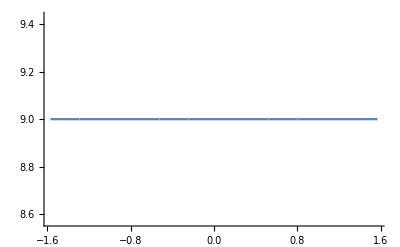

```mathematica
Plot[FI,{ϕ,-π/2,π/2}]
```

```mathematica
FI/.ϕ->0
```

9.

```mathematica
(*compare this to the variance*)
```

```mathematica
3/9
```

1/3